# Curso de Verão 2020 - Instituto de Física da USP

Ministrante: Alexandre Levine – Departamento de Física dos Materiais e Mecânica

Dias 10 a 14 – das 11h00 às 12h30

Local:

Minicurso “Técnicas para resolver problemas de física com Mathematica®”

Resumo: Nesse minicurso vamos aprender como resolver problemas de física básica e avançada com sistema de álgebra computacional Mathematica®. Vamos discutir seguintes tópicos: • Introdução aos sistemas de álgebra computacional, CAS

• Mecânica: oscilador harmónico, pêndulo físico

• Eletromagnetismo: Linhas de campo elétrico, partículas carregadas num campo eletromagnético, Leis de Ótica geométrica

• Mecânica Quântica: Pacotes de onda, Partícula em um poço potencial quadrático

• Transporte elétrico no regime clássico e quântico

Livro texto: P. T. Tam, A Physicist's Guide to Mathematica®. Os arquivos contem informações do livro e Wolfram Demonstration Project adotados por Marcela Babini , estudante de Mestrado IFUSP.

## AULA 1 - INTRODUÇÃO AO MATHEMATICA®

Mathematica é um software que pode ser aplicado em diversas áreas - o que o torna ideal, já que pode ser usado em diferentes momentos durante graduação, pós-graduação ou mercado de trabalho. Além de cálculos e gráficos em geral, usando Mathematica você também pode trabalhar com banco de dados e até fazer apresentações, tudo em um único programa. Neste curso, aprenderemos a abordar diferentes problemas em várias áreas da física. Para começar, vamos conhecer melhor a linguagem e os recursos que mais utilizamos de Mathematica.

## Regras básicas de linguagem

1. Os nomes das funções do Wolfram sempre iniciam com letra maiúscula;

2. [  ] são usados ao redor do que será calculado;

3.{  } são usadas para listas e limites;

4. Para realizar o cálculo, pressione Shift+Enter;

5. Para obter ajuda pressione tecla ‘F1’

Exemplos:

```mathematica
Prime [10]
```

29

```mathematica
Prime [10000000]
```

179424673

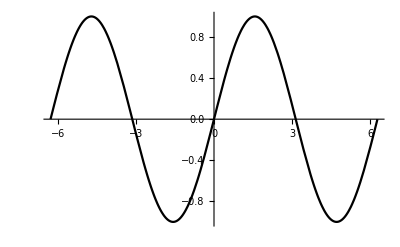

```mathematica
Plot[Sin[x], {x, -2π, 2π}]
```

Esse mesmo gráfico pode ser feito através do assistente do Mathematica. No menu Palettes, escolha a opção Classroom Assistant e, depois, Basic Commands. Na aba 2D, clique na opção Plot e depois em function. Aparecerá o texto abaixo:

Plot[function,{var,min,max}]

Usando a aba de funções em Basic Commands e Calculator, complete o texto assim:

```mathematica
Plot[Sin[x],{x,-2π,2π}]
```

-Graphics-

Temos o mesmo gráfico feito anteriormente, mas dessa vez sem a necessidade de decorar as funções usadas antes.

No Classroom Assistant, também é possível fazer formatações de texto para apresentações, como o que está sendo utilizado nesse documento.

#### Usos de ( ), [ ] e { }

```mathematica
(*Parênteses são usados para cálculos*)
1/(2.5 + 1.7^3)
```

0.134898

```mathematica
(*Colchetes são usados em funções*)
Sqrt[16]
```

4

```mathematica
(*Chaves são usadas para fazer listas ou determinar limites*)
{1, 3, 10}+{2, 4, 6}
```

{3,7,16}

### Exercício

Ache o número m que é a multiplicação  do 115∘ e do 312∘ números primos.

```mathematica
a=Prime[115]
```

631

```mathematica
b=Prime[312]
```

2069

```mathematica
m=a*b
```

1305539

Outro jeito de calcular:

```mathematica
m=(Prime[115]*Prime[312])
```

1305539

```mathematica
R= 6371009;
M=5.97x 10^24;
GN= 6.7x 10^-11;
m=80;
enerPot[r_]:= -GN*m*M/r;
Series[enerPot[r],{r, R,1}]
ap[r_]:=
Plot[enerPot[r], {r,R,20R}]
```

SetDelayed::write: Tag SeriesData in (-5.02263×10^9 x^2+788.357 x^2 (r-6371009)-0.000123741 x^2 (r-6371009)^2+O[r-6371009]^3)[r] is Protected.

$Failed

-Graphics-

## Polinómios

O Mathematica expande e fatora polinómios a partir dos comandos Expand e Factor. Use assim:

```mathematica
ClearAll["Global`*"]; (*Comando para limpar os valores dados a variáveis anteriormente. Importante para garantir que o cálculo será feito corretamente, mesmo repetindo as letras dedidacas a variáveis anteriormente*)
poli=(3 c+ b x+ a x^3)^2
```

(3 c+b x+a x^3)^2

```mathematica
Expand[poli]
```

9 c^2+6 b c x+b^2 x^2+6 a c x^3+2 a b x^4+a^2 x^6

```mathematica
Factor[%]
```

(3 c+b x+a x^3)^2

Note que podemos utilizar o símbolo % para nos referirmos a um resultado imediatamente anterior.

#### Exercício

Considere a fração (a-1)(b.b2-4b+4)/(b-2)^5. Vamos fazer a expansão do numerador e do denominador separadamente e, depois, junto. Em seguida, escreveremos o resultado novamente em forma de fração e vamos decompor em frações parciais. Por fim, vamos calcular o resultado numérico para a=7 e b=11.

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*Escrevendo a fração dada no exercício*)
(a-1)(b^2-4 b+4)/(b-2)^5
```

((-1+a) (4-4 b+b^2))/(-2+b)^5

```mathematica
ExpandNumerator[(a-1)(b^2-4 b+4)/(b-2)^5] (*Expande somente o numerador*)
```

(-4+4 a+4 b-4 a b-b^2+a b^2)/(-2+b)^5

```mathematica
ExpandDenominator[(a-1)(b^2-4 b+4)/(b-2)^5] (*Expande somente o denominador*)
```

((-1+a) (4-4 b+b^2))/(-32+80 b-80 b^2+40 b^3-10 b^4+b^5)

```mathematica
ExpandAll[(a-1)(b^2-4 b+4)/(b-2)^5] (*Expande toda a fração*)
```

-4/(-32+80 b-80 b^2+40 b^3-10 b^4+b^5)+(4 a)/(-32+80 b-80 b^2+40 b^3-10 b^4+b^5)+(4 b)/(-32+80 b-80 b^2+40 b^3-10 b^4+b^5)-(4 a b)/(-32+80 b-80 b^2+40 b^3-10 b^4+b^5)-b^2/(-32+80 b-80 b^2+40 b^3-10 b^4+b^5)+(a b^2)/(-32+80 b-80 b^2+40 b^3-10 b^4+b^5)

```mathematica
Apart[(a-1)(b^2-4 b+4)/(b-2)^5, a] (*Separa a fração em frações parciais de acordo com a variável escolhida*)
```

-1/(-2+b)^3+a/(-2+b)^3

```mathematica
Cancel[(a-1)(b^2-4 b+4)/(b-2)^5] (*Simplifica a fração*)
```

(-1+a)/(-2+b)^3

```mathematica
(a-1)(b^2-4 b+4)/(b-2)^5 /.{a-> 7, b-> 11} (*O símbolo /. atribui os valores numéricos às variáveis a e b nessa conta*)
```

2/243

## Equações

Para indicar equações, utilizamos o sinal de igual em dobro: ==

Também é possível resolver as equações com Mathematica, bem como sistemas de equações com o comando Solve. Observe os exemplos a seguir.

```mathematica
equation1=a x^2 + 7 b x+15 ==0
```

15+7 b x+a x^2==0

```mathematica
Solve[equation1, x]
```

{{x→(-7 b-√(-60 a+49 b^2))/(2 a)},{x→(-7 b+√(-60 a+49 b^2))/(2 a)}}

Um sistema de equações pode ser criado utilizando as {  }.

```mathematica
eqnlist1={a x^2+y==1, b y-x==15}
```

{a x^2+y==1,-x+b y==15}

```mathematica
Solve[eqnlist1, {x, y}]
```

{{x→(-1-√(1-60 a b+4 a b^2))/(2 a b),y→(30-1/(a b)-(√(1-60 a b+4 a b^2))/(a b))/(2 b)},{x→(-1+√(1-60 a b+4 a b^2))/(2 a b),y→(30-1/(a b)+(√(1-60 a b+4 a b^2))/(a b))/(2 b)}}

Também é possível escrever o sistema em termos dependentes somente de y, eliminando o x por meio do comando Eliminate.

```mathematica
Eliminate[eqnlist1, x]
```

-30 a b y+a b^2 y^2==1-225 a-y

#### Exercício

Vamos resolver a equação

x^4 +3 x^3+x^2-x =1

```mathematica
ClearAll["Global`*"];
eqn2=x^4+ 3 x^3+x^2-x==1
```

-x+x^2+3 x^3+x^4==1

```mathematica
NSolve[eqn2, x] (*Resolve a equação numericamente*)
```

{{x→-2.50507},{x→-0.592608-0.476565 ⅈ},{x→-0.592608+0.476565 ⅈ},{x→0.690284}}

```mathematica
(*Duas raízes são reais. Esse resultado pode ser útil em vários problemas físicos.*)
```

## Introdução a Ferramentas de Cálculo

#### Derivada

As derivadas podem ser calculadas utilizando a função D, seguido da expressão que se quer derivar, a variável e a ordem da derivada. O exemplo abaixo demonstra isso:

```mathematica
D[x^5, {x, 3}]
```

60 x^2

Também podemos escrever a derivada de uma função como:

```mathematica
deriv = Sin'[x]
```

Cos[x]

#### Definindo Funções do Usuário

Para definir suas próprias funções, o usuário do Mathematica pode usar o símbolo := (dois pontos seguido de igual). Por exemplo, se a intenção for definir uma função que retorne o quadrado de um valor qualquer, podemos criar uma função “square” tal que:

```mathematica
square[x_]:=x^2;
```

Agora podemos usar a função criada usando os critérios de funções do Mathematica:

```mathematica
square[146]
```

21316

#### Integral

Para integrar uma função, podemos utilizar o comando Integrate do Mathematica. Vamos criar uma função qualquer e integrá-la em seguida:

```mathematica
func[t_]:= a t^2 + t^3;
```

```mathematica
Integrate[func[x], x]
```

(a x^3)/3+x^4/4

## Lidando com Equações Diferenciais

Para resolver equações diferenciais, o Mathematica tem o comando DSolve, que resolve analiticamente equações diferenciais, a partir de condições iniciais pré-determinadas. Observe o exemplo a seguir.

```mathematica
ClearAll["Global`*"];
DSolve[x''[t]==x[t], x[t], t]
```

{{x[t]→ⅇ^t C[1]+ⅇ^-t C[2]}}

```mathematica
ClearAll["Global`*"];
(*Vamos criar uma equação diferencial de segunda ordem para esse exemplo*)
ode=x''[t] + x'[t] == t Sin [t]^2 Cos[t]
```

x'[t]+x''[t]==t Cos[t] Sin[t]^2

```mathematica
(*Agora, vamos incluir na função DSolve a expressão a ser resolvida, as condições iniciais para x e x' e as variáveis do problema*)
DSolve[{ode, x[0]==1, x'[0]==0}, x[t], t]
```

{{x[t]→-1/1800 ⅇ^-t (36-1400 ⅇ^t-450 ⅇ^t Cos[t]+225 ⅇ^t t Cos[t]+14 ⅇ^t Cos[3 t]-45 ⅇ^t t Cos[3 t]-225 ⅇ^t Sin[t]-225 ⅇ^t t Sin[t]+27 ⅇ^t Sin[3 t]+15 ⅇ^t t Sin[3 t])}}

Caso o intervalo em que se quer o resultado já esteja definido, podemos considerar também o cálculo do resultado numérico de uma equação diferencial. Exploraremos esse recurso nas próximas aulas.

## Introdução aos Recursos de Gráficos

Em vários momentos, nos estudos de física, plotar os resultados permite uma melhor análise do problema. Felizmente, Mathematica tem um robusto acervo de recursos para a produção de gráficos 2D, 3D e animações. Nesse exemplo básico, aprenderemos alguns dos recursos mais utilizados.

```mathematica
ClearAll["Global`*"];
(*Vamos criar a função que será representada no gráfico*)
function = Sin[x] Sin[3 x] Sin [5 x]
```

Sin[x] Sin[3 x] Sin[5 x]

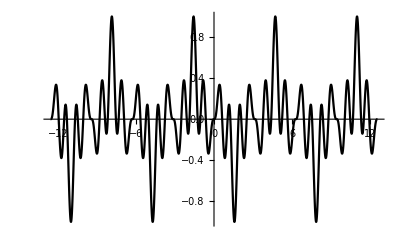

```mathematica
graph1=Plot[function, {x, -4π, 4π}]
```

```mathematica
(*Agora, vamos customizar o gráfico utilizando opções relacionadas ao comando Plot. Para saber todas as opções disponíveis, basta entrar com Options[Plot]*)
Options[Graphics3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→True,BoxRatios→Automatic,BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,SphericalRegion→False,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1}}

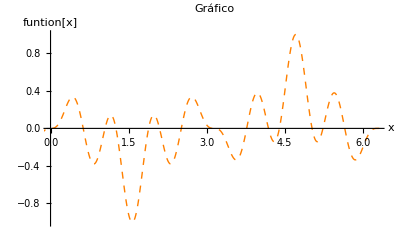

```mathematica
graph1 = Plot[ function,{x, -4π, 4π},PlotLabel -> "Gráfico", AxesLabel-> {"x", "funtion[x]"}, PlotRange-> {{0, 2π}, All}, PlotStyle-> {Orange, Dashed, Thick}]
```

### Cálculos Manipuláveis

O Mathematica permite que se faça cálculos e gráficos manipuláveis, que variam os resultados de acordo com as variáveis que são alteradas.

```mathematica
ClearAll["Global`*"];
SubPlus[a][f_]:=Simplify[-D[f,q]+q  f]
SubMinus[a][f_]:=Simplify[D[f,q]+q  f]
x̂[f_]:= (SubPlus[a][f]+SubMinus[a][f])/2
p̂[f_]:= (SubMinus[a][f]-SubMinus[a][f])/(2 ⅈ)

ψ0=(1/√π)^(1/2)Exp[-q^2/2];
ψ[n_,q_]:=Nest[SubPlus[a],ψ0,n]/Product[√(2(i+1)),{i,0,n-1}](*Nestpaclet:ref/Nest[f,expr,n] gives an expression with f applied n times to expr*)
Manipulate[ψ[n,q],{n,0,10,1}]
Manipulate[Integrate[ψ[n,q] x̂[x̂[ψ[n,q]]],{q,-∞,∞}],{n,0,5,1}]
```

```mathematica
(1+1)^2
```

4

```mathematica
(1 + 4)^2
```

25

```mathematica
(1 + 25)^2
```

676